```mathematica
Clear["Global`*"]
```

```mathematica
L=100;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

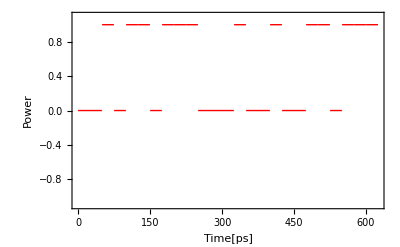

-1/(2 f π)ⅈ ⅇ^(-1250 ⅈ f π) (-1+ⅇ^(150 ⅈ f π)-ⅇ^(200 ⅈ f π)+ⅇ^(300 ⅈ f π)-ⅇ^(400 ⅈ f π)+ⅇ^(450 ⅈ f π)-ⅇ^(550 ⅈ f π)+ⅇ^(600 ⅈ f π)-ⅇ^(750 ⅈ f π)+ⅇ^(900 ⅈ f π)-ⅇ^(950 ⅈ f π)+ⅇ^(1050 ⅈ f π)-ⅇ^(1100 ⅈ f π)+ⅇ^(1150 ⅈ f π))

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
bit=25;
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25<t<(i+1)*25,1,0],If[i*25<t<(i+1)*25,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
∫_0^(bit*25) signal[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

Cos[400 π t]

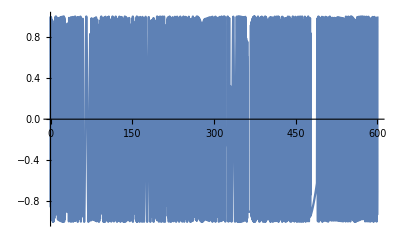

Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0])

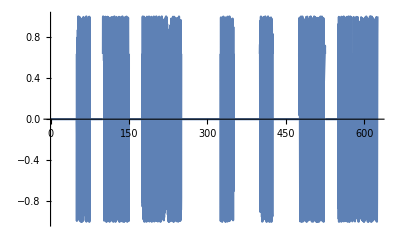

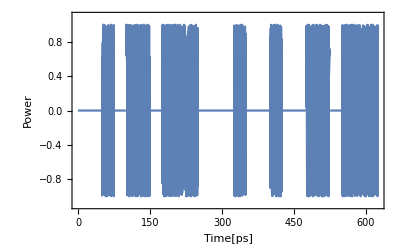

ⅈ Im[∫_0^625 ⅇ^(-2 ⅈ f π t1) cs[t1]ⅆt1]+Re[∫_0^625 ⅇ^(-2 ⅈ f π t1) cs[t1]ⅆt1]

```mathematica
Fc= 200 ;(*搬送波の周波数[THz]*)
carrier[t]= Cos[2*Pi*Fc*t]
Plot[carrier[t], {t,0,600}]
cs[t]=signal[t]*carrier[t]
Plot[Evaluate[cs[t]],{t,0,bit*25}]
Plot[Evaluate[cs[t]],{t,0,bit*25},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
ComplexExpand[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
```

```mathematica
Evaluate[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
ComplexExpand[Integratepaclet:ref/Integrate[cs[t]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,625}]]
Nintegrate[cs[t]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,625}]
```

∫_0^625 ⅇ^(-2 ⅈ f π t1) cs[t1]ⅆt1

Rule::rhs: パターンpaclet:ref/Integrateは規則System`ComplexExpandDump`reimexpr[RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) «1» (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+«5»+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),«1»]]→«1»の右辺にあります．

RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),{t,0,625}]

Nintegrate[ⅇ^(-2 ⅈ f π t1) Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),{t,0,625}]

```mathematica
Cs[ω]=ComplexExpand[FourierTransform[cs[t],t,ω]]
(*Cs[ω]:=1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω])*)
(*Plot[Re[FourierTransform[cs[t],t,ω]],{ω,-100,100}]*)
(*Plot[Evaluate[[Re[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]]],{f,-100,100}]*)
```

ⅈ ((ω Cos[50 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[75 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[100 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[150 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[175 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[250 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[325 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[350 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[400 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[425 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[475 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[525 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Cos[550 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Cos[650 ω])/(√(2 π) (-160000 π^2+ω^2)))-(ω Sin[50 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[75 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[100 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[150 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[175 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[250 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[325 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[350 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[400 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[425 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[475 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[525 ω])/(√(2 π) (-160000 π^2+ω^2))-(ω Sin[550 ω])/(√(2 π) (-160000 π^2+ω^2))+(ω Sin[650 ω])/(√(2 π) (-160000 π^2+ω^2))

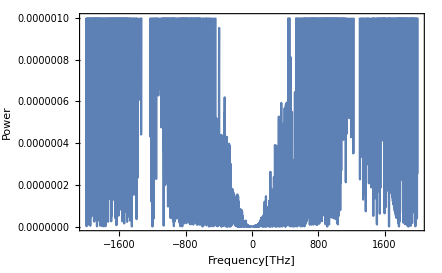

```mathematica
Plot[(Re[Cs[ω]]^2+Im[Cs[ω]]^2),{ω,-2*10^3,2*10^3},Frame->True,FrameLabel->{"Frequency[THz]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,10^-6}]
```

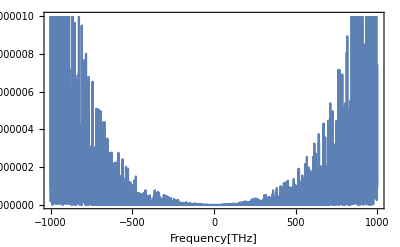

```mathematica
Plot[(Re[Cs[ω]]^2+Im[Cs[ω]]^2),{ω,-10^3,10^3},Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,10^-5}]
```

```mathematica
(*H_dis[ω]:=Exp[-1/2*I(ω-(2*Pi)*Fc)^2*β2*L]*)
(*cs_dis[t]=FourierTransform[H_dis[ω]*Cs[ω],ω,t,FourierParameters->{1,-1}]*)
```

```mathematica
cs_FT[t]=ComplexExpand[InverseFourierTransform[Cs[ω],ω,t]]
```

-1/4 Cos[400 π t] Sign[-650+t]-1/4 Cos[400 π t] Cos[800 π t] Sign[-650+t]+1/4 Cos[400 π t] Sign[-550+t]+1/4 Cos[400 π t] Cos[800 π t] Sign[-550+t]-1/4 Cos[400 π t] Sign[-525+t]-1/4 Cos[400 π t] Cos[800 π t] Sign[-525+t]+1/4 Cos[400 π t] Sign[-475+t]+1/4 Cos[400 π t] Cos[800 π t] Sign[-475+t]-1/4 Cos[400 π t] Sign[-425+t]-1/4 Cos[400 π t] Cos[800 π t] Sign[-425+t]+1/4 Cos[400 π t] Sign[-400+t]+1/4 Cos[400 π t] Cos[800 π t] Sign[-400+t]-1/4 Cos[400 π t] Sign[-350+t]-1/4 Cos[400 π t] Cos[800 π t] Sign[-350+t]+1/4 Cos[400 π t] Sign[-325+t]+1/4 Cos[400 π t] Cos[800 π t] Sign[-325+t]-1/4 Cos[400 π t] Sign[-250+t]-1/4 Cos[400 π t] Cos[800 π t] Sign[-250+t]+1/4 Cos[400 π t] Sign[-175+t]+1/4 Cos[400 π t] Cos[800 π t] Sign[-175+t]-1/4 Cos[400 π t] Sign[-150+t]-1/4 Cos[400 π t] Cos[800 π t] Sign[-150+t]+1/4 Cos[400 π t] Sign[-100+t]+1/4 Cos[400 π t] Cos[800 π t] Sign[-100+t]-1/4 Cos[400 π t] Sign[-75+t]-1/4 Cos[400 π t] Cos[800 π t] Sign[-75+t]+1/4 Cos[400 π t] Sign[-50+t]+1/4 Cos[400 π t] Cos[800 π t] Sign[-50+t]-1/4 Sign[-650+t] Sin[400 π t] Sin[800 π t]+1/4 Sign[-550+t] Sin[400 π t] Sin[800 π t]-1/4 Sign[-525+t] Sin[400 π t] Sin[800 π t]+1/4 Sign[-475+t] Sin[400 π t] Sin[800 π t]-1/4 Sign[-425+t] Sin[400 π t] Sin[800 π t]+1/4 Sign[-400+t] Sin[400 π t] Sin[800 π t]-1/4 Sign[-350+t] Sin[400 π t] Sin[800 π t]+1/4 Sign[-325+t] Sin[400 π t] Sin[800 π t]-1/4 Sign[-250+t] Sin[400 π t] Sin[800 π t]+1/4 Sign[-175+t] Sin[400 π t] Sin[800 π t]-1/4 Sign[-150+t] Sin[400 π t] Sin[800 π t]+1/4 Sign[-100+t] Sin[400 π t] Sin[800 π t]-1/4 Sign[-75+t] Sin[400 π t] Sin[800 π t]+1/4 Sign[-50+t] Sin[400 π t] Sin[800 π t]-(Sin[400 π t] Sign'[-650+t])/(1600 π)+(Cos[800 π t] Sin[400 π t] Sign'[-650+t])/(1600 π)-(Cos[400 π t] Sin[800 π t] Sign'[-650+t])/(1600 π)+(Sin[400 π t] Sign'[-550+t])/(1600 π)-(Cos[800 π t] Sin[400 π t] Sign'[-550+t])/(1600 π)+(Cos[400 π t] Sin[800 π t] Sign'[-550+t])/(1600 π)-(Sin[400 π t] Sign'[-525+t])/(1600 π)+(Cos[800 π t] Sin[400 π t] Sign'[-525+t])/(1600 π)-(Cos[400 π t] Sin[800 π t] Sign'[-525+t])/(1600 π)+(Sin[400 π t] Sign'[-475+t])/(1600 π)-(Cos[800 π t] Sin[400 π t] Sign'[-475+t])/(1600 π)+(Cos[400 π t] Sin[800 π t] Sign'[-475+t])/(1600 π)-(Sin[400 π t] Sign'[-425+t])/(1600 π)+(Cos[800 π t] Sin[400 π t] Sign'[-425+t])/(1600 π)-(Cos[400 π t] Sin[800 π t] Sign'[-425+t])/(1600 π)+(Sin[400 π t] Sign'[-400+t])/(1600 π)-(Cos[800 π t] Sin[400 π t] Sign'[-400+t])/(1600 π)+(Cos[400 π t] Sin[800 π t] Sign'[-400+t])/(1600 π)-(Sin[400 π t] Sign'[-350+t])/(1600 π)+(Cos[800 π t] Sin[400 π t] Sign'[-350+t])/(1600 π)-(Cos[400 π t] Sin[800 π t] Sign'[-350+t])/(1600 π)+(Sin[400 π t] Sign'[-325+t])/(1600 π)-(Cos[800 π t] Sin[400 π t] Sign'[-325+t])/(1600 π)+(Cos[400 π t] Sin[800 π t] Sign'[-325+t])/(1600 π)-(Sin[400 π t] Sign'[-250+t])/(1600 π)+(Cos[800 π t] Sin[400 π t] Sign'[-250+t])/(1600 π)-(Cos[400 π t] Sin[800 π t] Sign'[-250+t])/(1600 π)+(Sin[400 π t] Sign'[-175+t])/(1600 π)-(Cos[800 π t] Sin[400 π t] Sign'[-175+t])/(1600 π)+(Cos[400 π t] Sin[800 π t] Sign'[-175+t])/(1600 π)-(Sin[400 π t] Sign'[-150+t])/(1600 π)+(Cos[800 π t] Sin[400 π t] Sign'[-150+t])/(1600 π)-(Cos[400 π t] Sin[800 π t] Sign'[-150+t])/(1600 π)+(Sin[400 π t] Sign'[-100+t])/(1600 π)-(Cos[800 π t] Sin[400 π t] Sign'[-100+t])/(1600 π)+(Cos[400 π t] Sin[800 π t] Sign'[-100+t])/(1600 π)-(Sin[400 π t] Sign'[-75+t])/(1600 π)+(Cos[800 π t] Sin[400 π t] Sign'[-75+t])/(1600 π)-(Cos[400 π t] Sin[800 π t] Sign'[-75+t])/(1600 π)+(Sin[400 π t] Sign'[-50+t])/(1600 π)-(Cos[800 π t] Sin[400 π t] Sign'[-50+t])/(1600 π)+(Cos[400 π t] Sin[800 π t] Sign'[-50+t])/(1600 π)+ⅈ (1/4 Sign[-650+t] Sin[400 π t]+1/4 Cos[800 π t] Sign[-650+t] Sin[400 π t]-1/4 Sign[-550+t] Sin[400 π t]-1/4 Cos[800 π t] Sign[-550+t] Sin[400 π t]+1/4 Sign[-525+t] Sin[400 π t]+1/4 Cos[800 π t] Sign[-525+t] Sin[400 π t]-1/4 Sign[-475+t] Sin[400 π t]-1/4 Cos[800 π t] Sign[-475+t] Sin[400 π t]+1/4 Sign[-425+t] Sin[400 π t]+1/4 Cos[800 π t] Sign[-425+t] Sin[400 π t]-1/4 Sign[-400+t] Sin[400 π t]-1/4 Cos[800 π t] Sign[-400+t] Sin[400 π t]+1/4 Sign[-350+t] Sin[400 π t]+1/4 Cos[800 π t] Sign[-350+t] Sin[400 π t]-1/4 Sign[-325+t] Sin[400 π t]-1/4 Cos[800 π t] Sign[-325+t] Sin[400 π t]+1/4 Sign[-250+t] Sin[400 π t]+1/4 Cos[800 π t] Sign[-250+t] Sin[400 π t]-1/4 Sign[-175+t] Sin[400 π t]-1/4 Cos[800 π t] Sign[-175+t] Sin[400 π t]+1/4 Sign[-150+t] Sin[400 π t]+1/4 Cos[800 π t] Sign[-150+t] Sin[400 π t]-1/4 Sign[-100+t] Sin[400 π t]-1/4 Cos[800 π t] Sign[-100+t] Sin[400 π t]+1/4 Sign[-75+t] Sin[400 π t]+1/4 Cos[800 π t] Sign[-75+t] Sin[400 π t]-1/4 Sign[-50+t] Sin[400 π t]-1/4 Cos[800 π t] Sign[-50+t] Sin[400 π t]-1/4 Cos[400 π t] Sign[-650+t] Sin[800 π t]+1/4 Cos[400 π t] Sign[-550+t] Sin[800 π t]-1/4 Cos[400 π t] Sign[-525+t] Sin[800 π t]+1/4 Cos[400 π t] Sign[-475+t] Sin[800 π t]-1/4 Cos[400 π t] Sign[-425+t] Sin[800 π t]+1/4 Cos[400 π t] Sign[-400+t] Sin[800 π t]-1/4 Cos[400 π t] Sign[-350+t] Sin[800 π t]+1/4 Cos[400 π t] Sign[-325+t] Sin[800 π t]-1/4 Cos[400 π t] Sign[-250+t] Sin[800 π t]+1/4 Cos[400 π t] Sign[-175+t] Sin[800 π t]-1/4 Cos[400 π t] Sign[-150+t] Sin[800 π t]+1/4 Cos[400 π t] Sign[-100+t] Sin[800 π t]-1/4 Cos[400 π t] Sign[-75+t] Sin[800 π t]+1/4 Cos[400 π t] Sign[-50+t] Sin[800 π t]-(Cos[400 π t] Sign'[-650+t])/(1600 π)+(Cos[400 π t] Cos[800 π t] Sign'[-650+t])/(1600 π)+(Sin[400 π t] Sin[800 π t] Sign'[-650+t])/(1600 π)+(Cos[400 π t] Sign'[-550+t])/(1600 π)-(Cos[400 π t] Cos[800 π t] Sign'[-550+t])/(1600 π)-(Sin[400 π t] Sin[800 π t] Sign'[-550+t])/(1600 π)-(Cos[400 π t] Sign'[-525+t])/(1600 π)+(Cos[400 π t] Cos[800 π t] Sign'[-525+t])/(1600 π)+(Sin[400 π t] Sin[800 π t] Sign'[-525+t])/(1600 π)+(Cos[400 π t] Sign'[-475+t])/(1600 π)-(Cos[400 π t] Cos[800 π t] Sign'[-475+t])/(1600 π)-(Sin[400 π t] Sin[800 π t] Sign'[-475+t])/(1600 π)-(Cos[400 π t] Sign'[-425+t])/(1600 π)+(Cos[400 π t] Cos[800 π t] Sign'[-425+t])/(1600 π)+(Sin[400 π t] Sin[800 π t] Sign'[-425+t])/(1600 π)+(Cos[400 π t] Sign'[-400+t])/(1600 π)-(Cos[400 π t] Cos[800 π t] Sign'[-400+t])/(1600 π)-(Sin[400 π t] Sin[800 π t] Sign'[-400+t])/(1600 π)-(Cos[400 π t] Sign'[-350+t])/(1600 π)+(Cos[400 π t] Cos[800 π t] Sign'[-350+t])/(1600 π)+(Sin[400 π t] Sin[800 π t] Sign'[-350+t])/(1600 π)+(Cos[400 π t] Sign'[-325+t])/(1600 π)-(Cos[400 π t] Cos[800 π t] Sign'[-325+t])/(1600 π)-(Sin[400 π t] Sin[800 π t] Sign'[-325+t])/(1600 π)-(Cos[400 π t] Sign'[-250+t])/(1600 π)+(Cos[400 π t] Cos[800 π t] Sign'[-250+t])/(1600 π)+(Sin[400 π t] Sin[800 π t] Sign'[-250+t])/(1600 π)+(Cos[400 π t] Sign'[-175+t])/(1600 π)-(Cos[400 π t] Cos[800 π t] Sign'[-175+t])/(1600 π)-(Sin[400 π t] Sin[800 π t] Sign'[-175+t])/(1600 π)-(Cos[400 π t] Sign'[-150+t])/(1600 π)+(Cos[400 π t] Cos[800 π t] Sign'[-150+t])/(1600 π)+(Sin[400 π t] Sin[800 π t] Sign'[-150+t])/(1600 π)+(Cos[400 π t] Sign'[-100+t])/(1600 π)-(Cos[400 π t] Cos[800 π t] Sign'[-100+t])/(1600 π)-(Sin[400 π t] Sin[800 π t] Sign'[-100+t])/(1600 π)-(Cos[400 π t] Sign'[-75+t])/(1600 π)+(Cos[400 π t] Cos[800 π t] Sign'[-75+t])/(1600 π)+(Sin[400 π t] Sin[800 π t] Sign'[-75+t])/(1600 π)+(Cos[400 π t] Sign'[-50+t])/(1600 π)-(Cos[400 π t] Cos[800 π t] Sign'[-50+t])/(1600 π)-(Sin[400 π t] Sin[800 π t] Sign'[-50+t])/(1600 π))

```mathematica
Plot[cs_FT[t],{t,0,625}]
```

-Graphics-

```mathematica
(*FourierTransform[ⅇ^((0.-1.0196526687420762*^-21 ⅈ) (-400 π+ω)^2)*1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω]),ω,t,FourierParameters->{1,-1}]*)
```

```mathematica
Plot[cs_dis[t],{t,-100,100}]
```

-Graphics-